## Funkcje tworzące i transformaty

### Funkcje tworzące

W Mathematice funkcję tworzącą ciągu {a_n} wyznaczamy w następujący sposób:

```mathematica
GeneratingFunction[a[n],n,z];
```

```mathematica
P[z_]=GeneratingFunction[PDF[PoissonDistribution[λ],n],n,z]
```

ⅇ^((-1+z) λ)

Postać szeregu możemy zobaczyć używając funkcji Series

```mathematica
Series[P[z],{z,0,10}]
```

ⅇ^-λ+ⅇ^-λ λ z+1/2 ⅇ^-λ λ^2 z^2+1/6 ⅇ^-λ λ^3 z^3+1/24 ⅇ^-λ λ^4 z^4+1/120 ⅇ^-λ λ^5 z^5+1/720 ⅇ^-λ λ^6 z^6+(ⅇ^-λ λ^7 z^7)/5040+(ⅇ^-λ λ^8 z^8)/40320+(ⅇ^-λ λ^9 z^9)/362880+(ⅇ^-λ λ^10 z^10)/3628800+O[z]^11

Współczynnik przy wybranym składniku znajdziemy przy pomocy funkcji SeriesCoefficient

```mathematica
Table[SeriesCoefficient[P[z],{z,0,k}],{k,0,10}]
```

{ⅇ^-λ,ⅇ^-λ λ,1/2 ⅇ^-λ λ^2,1/6 ⅇ^-λ λ^3,1/24 ⅇ^-λ λ^4,1/120 ⅇ^-λ λ^5,1/720 ⅇ^-λ λ^6,(ⅇ^-λ λ^7)/5040,(ⅇ^-λ λ^8)/40320,(ⅇ^-λ λ^9)/362880,(ⅇ^-λ λ^10)/3628800}

Dla λ=1, prawdopodobieństwo, że zmienna losowa o rozkładzie Poissona przyjmie wartość 3 wynosi

```mathematica
SeriesCoefficient[P[z],{z,0,3}]/.λ->1.
```

0.0613132

Wartość oczekiwaną dla danego rozkładu możemy znaleźć licząc pochodną funkcji tworzącej w punkcie 1

```mathematica
D[P[z],z]/.z->1
```

λ

### Transformata Laplace’a

Transformatę Laplace’a Stieltjesa dystrybuanty rozkładu ciągłego dostaniemy wyznaczając transformatę Laplace’a jej gęstości

```mathematica
F[s_]=LaplaceTransform[PDF[ExponentialDistribution[μ],t],t,s]
```

μ/(s+μ)

Wartość oczekiwaną zmiennej losowej można obliczyć przy pomocy pochodnej transformaty

```mathematica
-D[F[s],s]/.s->0
```

1/μ

## Proces Poissona

```mathematica
M=PoissonProcess[λ]
```

PoissonProcess[λ]

Przykładowo wyznaczymy prawdopodobieństwo, że przez czas t proces Poissona z intensywnością λ wygeneruje mniej niż 4 zdarzenia

```mathematica
Probability[m[t]<4,m\[Distributed]M]
```

1/6 ⅇ^(-t λ) (6+6 t λ+3 t^2 λ^2+t^3 λ^3)

```mathematica
p[k_,t_]=PDF[M[t],k]
```

Piecewise[{{(ⅇ^(-t λ) (t λ)^k)/(k!), k≥0}, {0, True}}]

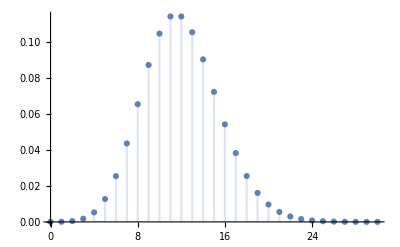

```mathematica
DiscretePlot[p[k,4]/.λ->3,{k,0,30}]
```

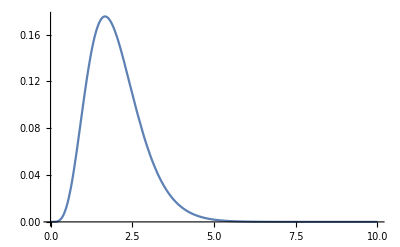

```mathematica
Plot[p[5,t]/.λ->3,{t,0,10}]
```

Generowanie procesu Poissona

```mathematica
proces=RandomFunction[M/.λ->3,{0,5}];
```

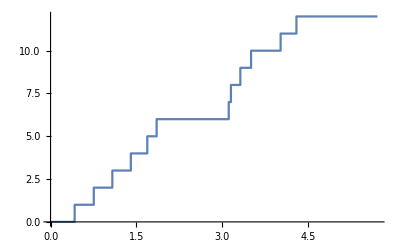

```mathematica
ListStepPlot[proces]
```

Czas pomiędzy zdarzeniami z procesu Poissona z parametrem λ ma rozkład wykładniczy z tym samym parametrem. Jeśli rozważamy dwa (ten wynik można uogólnić na większą liczbę procesów) procesy Poissona z intensywnościami λ i μ, to prawdopodobieństwo, że jako pierwsze nastąpiło zdarzenie np. z tego pierwszego procesu wynosi

```mathematica
Probability[X==Min[X,Y],{X\[Distributed]ExponentialDistribution[λ], Y\[Distributed]ExponentialDistribution[μ]}]
```

λ/(λ+μ)

### Zadania

1. Trzy razy dziennie kierowca parkuje swój samochód na pół godziny bez uiszczenia opłaty za
postój.Kontroler odwiedza każde miejsce postojowe zgodnie z procesem Poissona z parametrem λ (na godzinę).Jeśli natrafi na samochód, za który nie została wniesiona opłata, wystawia mandat.
(a) Jakie jest prawdopodobieństwo, że danego dnia kierowcy się upiecze?
(b) Jakie jest prawdopodobieństwo, że kierowca otrzyma w jednym dniu dwa mandaty?
(c) Załóżmy, że opłata za parkowanie wynosi 5 zł/h, a jednorazowa kara za nieopłacenie
miejsca wynosi 50 zł.Jaka jest wartość oczekiwana łącznej kary dla naszego niesfornego kierowcy?Jaka musiałaby być intensywność kontroli, żeby kierowcy opłacało się
ryzykować?

1. Ze względu na właściwości procesu Poissona, nie jest ważne, w jakich kawałkach kierowca parkuje samochód, istotny jest tylko łączny czas parkowania w ciągu dnia.

```mathematica
Kontrola = PoissonProcess[λ];
```

a) Szukane prawdopodobieństwo:

```mathematica
Probability[k[1.5]==0,k\[Distributed]Kontrola]
```

ⅇ^(-1.5 λ)

b) Prawdopodobieństwo, że kierowca dostanie dwa mandaty wynosi:

```mathematica
Probability[m[1.5]==2,m\[Distributed]Kontrola]
```

1.125 ⅇ^(-1.5 λ) λ^2

c) Wartość oczekiwana kary w ciągu dnia to

```mathematica
kara[λ_]=Expectation[50 m[1.5], m\[Distributed]Kontrola]
```

75. λ

Żeby ryzyko było opłacalne, wartość oczekiwana kary nie powinna przekroczyć zaoszczędzonej kwoty

```mathematica
Reduce[{kara[λ]<5*1.5,λ>0}, λ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<λ<0.1

2. Student wychodzi z zajęć o losowej godzinie między 16 : 00 a 17 : 00. Do domu dojechać może
jednym z dwóch autobusów, A i B.Autobus A odjeżdża regularnie co 10 min., a autobus B
zgodnie z procesem Poissona z tą samą częstością.Zakładając, że student zawsze wybiera
autobus, który pojawi się wcześniej, jakie jest prawdopodobieństwo, że danego dnia pojedzie
do domu autobusem A?

2. Przez A i B oznaczymy rozkłady czasu oczekiwania na każdy autobusów.

```mathematica
A=UniformDistribution[{0,10}];
B=ExponentialDistribution[1/10];
```

```mathematica
Probability[a<b,{a\[Distributed]A, b\[Distributed]B}]//N
```

0.632121

3. Pieszy chce przejść przez ulicę dwukierunkową.Z obu stron samochody nadjeżdżają zgodnie
z procesem Poissona z intensywnościami λ1 z lewej i λ2 z prawej strony.Przejście możliwe
jest, jeśli przez czas T z żadnej ze stron nie nadjedzie samochód.
(a) Jakie jest prawdopodobieństwo, że pieszy nie będzie musiał czekać na przejście?
(b) Jakie jest prawdopodobieństwo, że pierwszy samochód nadjedzie z lewej strony?
(c) Jaki jest rozkład liczby samochodów, które miną pieszego zanim ten będzie mógł bezpiecznie przejść na drugą stronę?

4. Zgłoszenia napływają do serwera zgodnie z procesem Poissona z parametrem λ.
(a) Dla wartości λ = 2, 4, 6, 8 [/min] oblicz i przedstaw w tabeli i w formie graficznej prawdopodobieństwo, że w ciągu dwóch minut pojawi się k (=0,...,10) zgłoszeń.
(b) Dla wartości λ z (a) i t=0.1, 0.2, ..., 1 przedstaw w tabeli i w formie graficznej prawdopodobieństwa, że odstęp pomiędzy kolejnymi zgłoszeniami będzie mniejsza niż t
(c) Dla tych samych λ przedstaw w formie graficznej rozkład czasu do pojawienia się 5, 10, 15, i 20 zgłoszeń.